### Hamiltonian matrix for lattice in 2 site case

```mathematica
SetDirectory[NotebookDirectory[]];
kinetic = Import["211_t.dat"];
interaction =  Import["211_U.dat"];
energy = t kinetic+U interaction;
MatrixForm[energy]
MatrixForm[Transpose[Eigenvectors[energy]]]
MatrixForm[Eigenvalues[energy]]
```

(U | t | -t | 0
t | 0 | 0 | t
-t | 0 | 0 | -t
0 | t | -t | U)

(0 | -1 | 1 | 1
1 | 0 | -U/(4 t)-(√(16 t^2+U^2))/(4 t) | -U/(4 t)+(√(16 t^2+U^2))/(4 t)
1 | 0 | -(-U-√(16 t^2+U^2))/(4 t) | -(-U+√(16 t^2+U^2))/(4 t)
0 | 1 | 1 | 1)

(0
U
1/2 (U-√(16 t^2+U^2))
1/2 (U+√(16 t^2+U^2)))

#### Series expansion for small t

```mathematica
e= Eigenvalues[energy];
Assuming[U>0 ,Series[e[[3]],{t,0,2}]]
Assuming[U>0 ,Series[e[[4]],{t,0,2}]]
```

-(4 √(U^2) t^2)/U^2+O[t]^3

1/2 (U+√(U^2))+(4 √(U^2) t^2)/U^2+O[t]^3

### Make some plot of the eigenvalues and eigenvectors as a function of x=U/t (set t =1 in the expressions above)

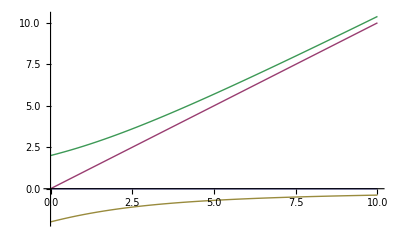

```mathematica
Plot[{0,x,1/2(x-√(16+x^2)),1/2(x+√(16+x^2))},{x,0,10}]
```